## Parameters

Parameters here are normalized by the incident wavelength

```mathematica
λ=1;(*the wavelelength of the incident wave*)
k0=(2π)/λ;(*wavevector*)
L=0.5;(*grating period*)
ff=5/6;(*grating filling factor (metal)*)
d=ff L;(*the part of the grating filled with metal*)
θ=0;(*angle of incidence*)
nn=300;(*to definition of the number of the evanescent modes above the grating*)
ns=2 nn;(*to definition of the number of the evanescent modes in the slit*)

η=Function[τ1,If[τ1==0,2,1]];
kx=k0 Sin[θ];(*x component of the wavevector*)
φ[n_Integer]:=kx+2 π/L n;
MSqrt[zz_]:=√ⅈ Sqrt[-ⅈ zz];(*function for the square root with a chosen branch*)
NSqrt[zz_]:=I Conjugate[Sqrt[Conjugate[-zz]]];(*function for the square root with a chosen branch*)
wL=(L-d)/L;(*useful parameter*)
wLs=(L+d)/L;(*useful parameter*)
woL=2π wL;(*useful parameter*)
kxw=kx(L-d);(*useful parameter*)

h0=0.9167251185043579;(*the slit height*)
(*The slit grating problem was solve with a home-made code, with field functions declared below. Here we use amplitudes computed with this code.*)
F=Table[KroneckerDelta[0,n],{n,-nn,nn}];(*the amplitude of the incident wave*)
Reflection=ToExpression[Import["path\\Reflection.dat","Data"]];(*the amplitudes of the reflected waves*)
Transmission=ToExpression[Import["path\\Transmission.dat","Data"]];(*the amplitudes of the transmitted waves*)
AmS=ToExpression[Import["path\\AsAmp.dat","Data"]];(*the amplitudes of waves in the slit*)
BmS=ToExpression[Import["path\\BsAmp.dat","Data"]];(*the amplitudes of waves in the slit*)
```

In this code, we define the slit grating in the following way.
The corner of the first metal bar at the coordinate x=0, and its another corner at x=d= ff*L.
Then the slit starts at x=d= ff*L and ends at x=L.
Then repeat (the period is L).

## Fields

Here we declare the functions for the electric and magnetic fields.
Designations: Hy - the y-component of the magnetic field, Ex - the x-component of the electric field, Ez - the z-component of the electric field,
Ar - the region above the grating, At - the region below the grating, G - the grating region.

```mathematica
HyAr[x_,z_]:=N[Sum[(F[[n+nn+1]]Exp[-ⅈ Sqrt[k0^2-φ[n]^2]z]+Reflection[[n+nn+1]]Exp[ⅈ Sqrt[k0^2-φ[n]^2]z])Exp[ⅈ φ[n]x],{n,-nn,nn}]][[1]];
ExAr[x_,z_]:=N[Sum[Sqrt[1-(φ[m]/k0)^2](-F[[m+nn+1]]Exp[-ⅈ Sqrt[k0^2-φ[m]^2]z]+Reflection[[m+nn+1]]Exp[ⅈ Sqrt[k0^2-φ[m]^2]z])Exp[ⅈ φ[m]x],{m,-nn,nn}]][[1]];
EzAr[x_,z_]:=-N[Sum[φ[m]/k0(F[[m+nn+1]]Exp[-ⅈ NSqrt[k0^2-φ[m]^2]z]+Reflection[[m+nn+1]]Exp[ⅈ NSqrt[k0^2-φ[m]^2]z])Exp[ⅈ φ[m]x],{m,-nn,nn}]][[1]];

HyAt[x_,z_]:=N[Sum[Transmission[[n+nn+1]]Exp[-ⅈ NSqrt[k0^2-φ[n]^2](z+h0)]Exp[ⅈ φ[n]x],{n,-nn,nn}]][[1]];
ExAt[x_,z_]:=-N[Sum[Sqrt[1-(φ[m]/k0)^2]Transmission[[m+nn+1]]Exp[-ⅈ Sqrt[k0^2-φ[m]^2](z+h0)]Exp[ⅈ φ[m]x],{m,-nn,nn}]][[1]];
EzAt[x_,z_]:=-N[Sum[φ[m]/k0 Transmission[[m+nn+1]]Exp[-ⅈ NSqrt[k0^2-φ[m]^2](z+h0)]Exp[ⅈ φ[m]x],{m,-nn,nn}]][[1]]; 
qS[s_]:=(π s)/(L-d);(*auxiliary function*)
kzS[s_]:=MSqrt[k0^2-((π s)/(L-d))^2];(*auxiliary function*)
kzSok0[s_]:=MSqrt[1-((π s)/(k0(L-d)))^2];(*auxiliary function*)
HyG[x_,z_]:=N[Sum[(AmS[[s+1]] Exp[-ⅈ kzS[s]z]+BmS[[s+1]]Exp[ⅈ kzS[s](z+h0)])Cos[qS[s](x-d)],{s,0,ns}]][[1]];
ExG[x_,z_]:=N[Sum[kzSok0[s](-AmS[[s+1]] Exp[-ⅈ kzS[s]z]+BmS[[s+1]]Exp[ⅈ kzS[s](z+h0)])Cos[qS[s](x-d)],{s,0,ns}]][[1]];
EzG[x_,z_]:=-N[ⅈ Sum[qS[s]/k0 Sin[qS[s](x-d)](AmS[[s+1]] Exp[-ⅈ kzS[s]z]+BmS[[s+1]]Exp[ⅈ kzS[s](z+h0)]),{s,0,ns}]][[1]];
hyAr[t_,x_,z_]:= Re[HyAr[x,z] Exp[-ⅈ k0 t]];
exAr[t_,x_,z_]:= Re[ExAr[x,z] Exp[-ⅈ k0 t]];
ezAr[t_,x_,z_]:= Re[EzAr[x,z] Exp[-ⅈ k0 t]];
hyG[t_,x_,z_]:= Re[HyG[x,z] Exp[-ⅈ k0 t]];
exG[t_,x_,z_]:= Re[ExG[x,z] Exp[-ⅈ k0 t]];
ezG[t_,x_,z_]:= Re[EzG[x,z] Exp[-ⅈ k0 t]];
hyAt[t_,x_,z_]:= Re[HyAt[x,z] Exp[-ⅈ k0 t]];
exAt[t_,x_,z_]:= Re[ExAt[x,z] Exp[-ⅈ k0 t]];
ezAt[t_,x_,z_]:= Re[EzAt[x,z] Exp[-ⅈ k0 t]];
(*the signes are very important, here we define functions based on the fields according to spaghetti equations in the paper*)
ftAr[t_,x_,z_]:=-hyAr[t,x,z];
fxAr[t_,x_,z_]:=ezAr[t,x,z];
fzAr[t_,x_,z_]:=-exAr[t,x,z];
ftG[t_,x_,z_]:=-hyG[t,x,z];
fxG[t_,x_,z_]:=ezG[t,x,z];
fzG[t_,x_,z_]:=-exG[t,x,z];
ftAt[t_,x_,z_]:=-hyAt[t,x,z];
fxAt[t_,x_,z_]:=ezAt[t,x,z];
fzAt[t_,x_,z_]:=-exAt[t,x,z];
XC=d+(L-d)/2(*the center of the slit*)
```

0.458333

Checking the fields values at  the middle plane of a slit, x=x_c.

```mathematica
Table[ezAr[t,XC,z],{t,0,1,0.1},{z,0,0.5,0.1}]//Quiet//Chop
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
Table[ezG[t,XC,z],{t,0,1,0.1},{z,0,-0.5,-0.1}]//Quiet//Chop
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
Table[ezAt[t,XC,z],{t,0,1,0.1},{z,-h0,-h0-0.5,-0.1}]//Quiet//Chop
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

## Computation of the electric flux over the half of period for the x-central plane

Here we find the initial values for ZEFS cut lines in the way that the flux values between them are equal.
For this at first we define the flux  as  a function of the t or the z coordinate (x=x_c) and then find the coordinates with equiflux step.

```mathematica
(*function definition*)
elFlintAr[z_,t1_,t2_]:= Re[HyAr[XC,z] ⅈ/k0( Exp[-ⅈ k0 t2]- Exp[-ⅈ k0 t1])];
elFlinzAr[t_,z1_,z2_]:= Re[NIntegrate[ExAr[XC,zn]Exp[-ⅈ k0 t],{zn,z1,z2}]];
elFliAPaR[t1_,t2_,z1_,z2_]:=elFlintAr[z1,t1,t2]+elFlinzAr[t2,z1,z2]
elFlintG[z_,t1_,t2_]:= Re[HyG[XC,z] ⅈ/k0( Exp[-ⅈ k0 t2]- Exp[-ⅈ k0 t1])];
elFlinzG[t_,z1_,z2_]:= Re[NIntegrate[ExG[XC,zn]Exp[-ⅈ k0 t],{zn,z1,z2}]];
(*coordinate computation*)
(*we already know the z values (centZ0 and centZ1) for the center of spaghetti circles, but they are not critical for ES building. the procedure allowong to define these valueas is provided below.*)
centZ0=-0.209392718694389;
centZ1=-0.7094062531865826;
ftimi=FindMinimum[elFlintG[centZ0,0,t],{t,0.01,-0.1,0.1}];//Quiet(*minimum el fl value*)
ftima=FindMaximum[elFlintG[centZ0,0,t],{t,0.5,0.4,0.6}];//Quiet(*maximum el fl value*)
tt0=ftimi[[2,1,2]];(*shift el fl value from 0 on t axis (i.e. from the middle of period as the period is 1)*)
ffmax=ftima[[1]];(*maximum el fl value*)
ffmin=ftimi[[1]];(*minimumel fl value*)
ffmax=ffmax-ffmin ; (*max el fl value after shift to make minimum exactly 0*)
δfiE=ffmax/12;(*unit value of electric flux which is used as a step*)

ftimi1=FindMinimum[elFlintG[centZ1,0,t],{t,0.5,0.4,0.6}];//Quiet(*minimum el fl value*)
ftima1=FindMaximum[elFlintG[centZ1,0,t],{t,0.01,-0.1,0.1}];//Quiet(*maximum el fl value*)
tt01=ftima1[[2,1,2]];(*shift el fl value from 0 on t axis (i.e. from the middle of period as the period is 1)*)
ffmax1=ftima1[[1]];(*maximum el fl value*)
ffmin1=ftimi1[[1]];(*minimumel fl value*)

τ0={tt0}~Join~Table[FindRoot[elFlintG[centZ0,0,t]-ffmin-i δfiE==0,{t,λ/8,tt0,λ/2-tt0}][[1,2]],{i,1,12}]; //Quiet(*start points for red lines comctruction at the upper half*)
Table[elFlintG[centZ0,0,τ0[[i]]]-ffmin,{i,1,Length[τ0]}]/δfiE//Quiet//Chop
τ1={tt01}~Join~Table[FindRoot[elFlintG[centZ1,0,t]-ffmax1+i δfiE==0,{t,λ/8,tt0,λ/2}][[1,2]],{i,1,12}];//Quiet(*start points for red lines comctruction at the bottom half*)
Table[elFlintG[centZ1,0,τ1[[i]]]-ffmax1,{i,1,Length[τ0]}]/δfiE//Quiet//Chop
```

{0,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.}

{0,-1.,-2.,-3.,-4.,-5.,-6.,-7.,-8.,-9.,-10.,-11.,-12.}

## Build Red Lines

Constriction of the red ZEFS cut lines in a grating slit.

```mathematica
plstylm={Hue[0.93],Thickness[0.004]};(*a graphic style*)
sfg=0;(*auxiliary value*)
Clear[MSPG];
sissi=-1;(*a constant which defines ES direction*)
 (*MSPG contains a set of ZEFS cut lines found as a solution of the system of the differential equations. A line stops if it reaches one of the grating-air interface with command "StopIntegration". Mathematica give some errors but them does not influence the solution.*)
MSPG=Table[{NDSolve[{tg'[sg]==sissi fzG[tg[sg],xg[sg],zg[sg]],xg'[sg]==0,zg'[sg]==sissi ftG[tg[sg],xg[sg],zg[sg]],tg[0]==τ0[[i]],xg[0]==XC,zg[0]==centZ0, WhenEvent[zg[sg]>10^-7∨zg[sg]<-h0,end=sg;sfg=sg;"StopIntegration"]},{tg,xg,zg},{sg,0,0.5}],sfg},{i,1,Length[τ0]}];
MSPG[[8,2]]=0.0526711668758752;
Do[MSPG[[i,2]]=0.5,{i,1,5}];Do[MSPG[[i,2]]=0.5,{i,9,Length[MSPG]}];
sfg=0;
Clear[MSPG0];
sissi=1; MSPG0=Table[{NDSolve[{tg'[sg]==sissi fzG[tg[sg],xg[sg],zg[sg]],xg'[sg]==0,zg'[sg]==sissi ftG[tg[sg],xg[sg],zg[sg]],tg[0]==τ0[[i+5]],xg[0]==XC,zg[0]==centZ0, WhenEvent[zg[sg]>10^-7∨zg[sg]<-h0,end=sg;sfg=sg;"StopIntegration"]},{tg,xg,zg},{sg,0,0.5}],sfg},{i,1,3}];
MSPG0[[1,2]]=0.27063847820510484;
MSPG0[[2,2]]=0.21592840015283035;
MSPG0[[3,2]]=0.27077218408138887;
sfg=0;
Clear[MSPG1];
sissi=-1; MSPG1=Table[{NDSolve[{tg'[sg]==sissi fzG[tg[sg],xg[sg],zg[sg]],xg'[sg]==0,zg'[sg]==sissi ftG[tg[sg],xg[sg],zg[sg]],tg[0]==τ1[[i]],xg[0]==XC,zg[0]==centZ1, WhenEvent[zg[sg]>10^-7∨zg[sg]<-h0,end=sg;sfg=sg;"StopIntegration"]},{tg,xg,zg},{sg,0,0.5}],sfg},{i,1,Length[τ1]}];
MSPG1[[7,2]]=0.049361051938096305;
MSPG1[[8,2]]=0.05211072818494881;
Do[MSPG1[[i,2]]=0.5,{i,1,5}];Do[MSPG1[[i,2]]=0.5,{i,9,Length[MSPG]}];
sfg=0;
Clear[MSPG10];
sissi=1; MSPG10=Table[{NDSolve[{tg'[sg]==sissi fzG[tg[sg],xg[sg],zg[sg]],xg'[sg]==0,zg'[sg]==sissi ftG[tg[sg],xg[sg],zg[sg]],tg[0]==τ1[[i+5]],xg[0]==XC,zg[0]==centZ1, WhenEvent[zg[sg]>10^-7∨zg[sg]<-h0,end=sg;sfg=sg;"StopIntegration"]},{tg,xg,zg},{sg,0,0.5}],sfg},{i,1,3}];
MSPG10[[3,2]]=0.2705206411361013;
```

Plot

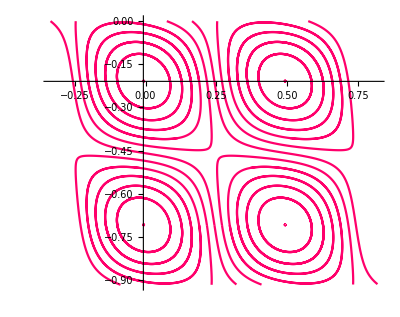

```mathematica
pl0=Show[Table[ParametricPlot[Evaluate[{tg[s],zg[s]}/.MSPG[[i,1,1]]],{s,0,MSPG[[i,2]]},PlotStyle->plstylm],{i,1,Length[MSPG]}],Table[ParametricPlot[Evaluate[{tg[s],zg[s]}/.MSPG0[[i,1,1]]],{s,0,MSPG0[[i,2]]},PlotStyle->plstylm],{i,1,Length[MSPG0]}],Table[ParametricPlot[Evaluate[{tg[s],zg[s]}/.MSPG1[[i,1,1]]],{s,0,MSPG1[[i,2]]},PlotStyle->plstylm],{i,1,Length[MSPG1]}],Table[ParametricPlot[Evaluate[{tg[s],zg[s]}/.MSPG10[[i,1,1]]],{s,0,MSPG10[[i,2]]},PlotStyle->plstylm],{i,1,Length[MSPG10]}],PlotRange->All]
```

Constriction of the red ZEFS cut lines in air.

```mathematica
(*In order to continue lines which stop at the grating-air interface, we keep coordinates where they stoped.
Here we find coordinates at the top interface.*)
mspinArzp={{(tg[MSPG[[6,2]]]/.MSPG[[6,1,1]]),(zg[MSPG[[6,2]]]/.MSPG[[6,1,1]])},{(tg[MSPG[[7,2]]]/.MSPG[[7,1,1]]),(zg[MSPG[[7,2]]]/.MSPG[[7,1,1]])},{(tg[MSPG[[8,2]]]/.MSPG[[8,1,1]]),(zg[MSPG[[8,2]]]/.MSPG[[8,1,1]])},{tg[MSPG10[[2,2]]],zg[MSPG10[[2,2]]]}/.MSPG10[[2,1,1]]};
(*Solution of differential equations in air above the slits*)
sf=0;
Clear[MSPAR];
sissi=-1; 
MSPAR=Table[{NDSolve[{t'[s]==sissi fzAr[t[s],x[s],z[s]],x'[s]==0,z'[s]==sissi ftAr[t[s],x[s],z[s]],t[0]==mspinArzp[[i,1]],x[0]==XC ,z[0]==mspinArzp[[i,2]], WhenEvent[z[s]<-10^-5,end=s;sf=s;"StopIntegration"]},{t,x,z},{s,0,0.5}],sf},{i,1,Length[mspinArzp]-1}];
sissi=1; 
MSPAR=Join[MSPAR,{{NDSolve[{t'[s]==sissi fzAr[t[s],x[s],z[s]],x'[s]==0,z'[s]==sissi ftAr[t[s],x[s],z[s]],t[0]==mspinArzp[[4,1]],x[0]==XC ,z[0]==mspinArzp[[4,2]], WhenEvent[z[s]<-10^-5,end=s;sf=s;"StopIntegration"]},{t,x,z},{s,0,0.5}],0}}];
MSPAR[[2,2]]=0.5;MSPAR[[4,2]]=0.5;
(*In order to continue lines which stop at the grating-air interface, we keep coordinates where they stoped.
Here we find coordinates at the bottom interface.*)
mspinArzp1={{tg[MSPG1[[6,2]]],zg[MSPG1[[6,2]]]}/.MSPG1[[6,1,1]],{tg[MSPG1[[7,2]]],zg[MSPG1[[7,2]]]}/.MSPG1[[7,1,1]],{tg[MSPG1[[8,2]]],zg[MSPG1[[8,2]]]}/.MSPG1[[8,1,1]],{tg[MSPG0[[2,2]]],zg[MSPG0[[2,2]]]}/.MSPG0[[2,1,1]]};
(*Solution of differential equations in air below the slits*)
sf=0;
Clear[MSPAR1];
sissi=-1; 
MSPAR1=Table[{NDSolve[{t'[s]==sissi fzAt[t[s],x[s],z[s]],x'[s]==0,z'[s]==sissi ftAt[t[s],x[s],z[s]],t[0]==mspinArzp1[[i,1]],x[0]==XC ,z[0]==mspinArzp1[[i,2]], WhenEvent[z[s]<-10^-5,end=s;sf=s;"StopIntegration"]},{t,x,z},{s,0,0.5}],sf},{i,1,Length[mspinArzp1]-1}];

sissi=1; 
MSPAR1=Join[MSPAR1,{{NDSolve[{t'[s]==sissi fzAt[t[s],x[s],z[s]],x'[s]==0,z'[s]==sissi ftAt[t[s],x[s],z[s]],t[0]==mspinArzp1[[4,1]],x[0]==XC ,z[0]==mspinArzp1[[4,2]], WhenEvent[z[s]<-10^-5,end=s;sf=s;"StopIntegration"]},{t,x,z},{s,0,0.5}],0}}];
Do[MSPAR1[[i,2]]=0.5,{i,1,4}];
MSPAR1[[1,2]]=FindMinimum[t[s]/.MSPAR1[[1,1,1]],{s,0.15,0.1,0.25}][[2,1,2]];
MSPAR1[[3,2]]=FindMaximum[(t[s]/.MSPAR1[[3,1,1]]),{s,0.19,0.16,0.25}][[2,1,2]];
```

Plot

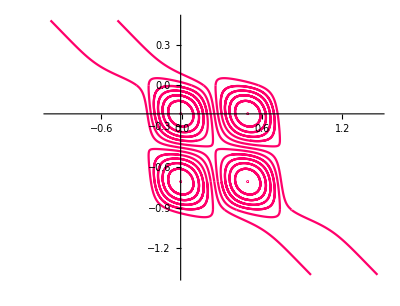

```mathematica
pl1=Show[pl0,Table[ParametricPlot[Evaluate[{t[s],z[s]}/.MSPAR[[i,1,1]]],{s,0,MSPAR[[i,2]]},PlotStyle->plstylm],{i,1,Length[MSPAR]}],Table[ParametricPlot[Evaluate[{t[s],z[s]}/.MSPAR1[[i,1,1]]],{s,0,MSPAR1[[i,2]]},PlotStyle->plstylm],{i,1,Length[MSPAR1]}],PlotRange->All]
```

## ES lines

In order to define some beginning points of ES we use the property that ES lines coincide with ZEFS cut lines along light lines. Thus, we find tangential touch point where red lines are parallel to light lines .

```mathematica
(*ES beginning points definition. For simplisity they're separated into a few sets, according to a set of ZEFS lines  to which these points belong.*)
pffm1=Table[FindMaximum[{((tg[s]/.MSPG[[i,1,1]])-(zg[s]/.MSPG[[i,1,1]])),0.1≤s≤0.3},{s,0.2}][[2,1,2]],{i,1,5}]~Join~{FindMaximum[{((tg[s]/.MSPG0[[1,1,1]])-(zg[s]/.MSPG0[[1,1,1]])),0≤s≤0.2},{s,0.07}][[2,1,2]]};
tZCESp1=Table[{tg[pffm1[[i]]]/.MSPG[[i,1,1]],zg[pffm1[[i]]]/.MSPG[[i,1,1]]},{i,1,5}]~Join~{{(tg[pffm1[[6]]]/.MSPG0[[1,1,1]]),(zg[pffm1[[6]]]/.MSPG0[[1,1,1]])}};
pffm2=Table[FindMaximum[{((tg[s]/.MSPG[[i,1,1]])-(zg[s]/.MSPG[[i,1,1]])),0.1≤s≤0.3},{s,0.2}][[2,1,2]],{i,9,13}]~Join~{FindMaximum[{((tg[s]/.MSPG0[[3,1,1]])-(zg[s]/.MSPG0[[3,1,1]])),0≤s≤0.2},{s,0.1}][[2,1,2]]}~Join~{FindMinimum[{((tg[s]/.MSPG[[12,1,1]])+(zg[s]/.MSPG[[12,1,1]])),0.1≤s≤0.3},{s,0.2}][[2,1,2]]};
tZCESp2=Table[{tg[pffm2[[i]]]/.MSPG[[i+8,1,1]],zg[pffm2[[i]]]/.MSPG[[i+8,1,1]]},{i,1,5}]~Join~{{(tg[pffm2[[6]]]/.MSPG0[[3,1,1]]),(zg[pffm2[[6]]]/.MSPG0[[3,1,1]])},{(tg[pffm2[[7]]]/.MSPG[[12,1,1]]),(zg[pffm2[[7]]]/.MSPG[[12,1,1]])}};
pffm3=Table[FindMaximum[{((tg[s]/.MSPG[[i,1,1]])+(zg[s]/.MSPG[[i,1,1]])),0.02≤s≤0.3},{s,0.2}][[2,1,2]],{i,9,12}]~Join~{FindMaximum[{((tg[s]/.MSPG0[[3,1,1]])+(zg[s]/.MSPG0[[3,1,1]])),0.2≤s≤MSPG0[[3,2]]},{s,0.25}][[2,1,2]]};
tZCESp3=Table[{tg[pffm3[[i]]]/.MSPG[[i+8,1,1]],zg[pffm3[[i]]]/.MSPG[[i+8,1,1]]},{i,1,4}]~Join~{{tg[pffm3[[5]]]/.MSPG0[[3,1,1]],zg[pffm3[[5]]]/.MSPG0[[3,1,1]]}};
pffm4=Table[FindMinimum[{((tg[s]/.MSPG[[i,1,1]])-(zg[s]/.MSPG[[i,1,1]])),0.≤s≤0.3},{s,0.05}][[2,1,2]],{i,9,13}]~Join~{FindMaximum[{(tg[s]/.MSPG10[[2,1,1]])+(zg[s]/.MSPG10[[2,1,1]]),0.1≤s≤MSPG10[[2,2]]},{s,0.2}][[2,1,2]]};
tZCESp4=Table[{tg[pffm4[[i]]]/.MSPG[[i+8,1,1]],zg[pffm4[[i]]]/.MSPG[[i+8,1,1]]},{i,1,5}]~Join~{{(tg[pffm4[[6]]]/.MSPG10[[2,1,1]])+1,(zg[pffm4[[6]]]/.MSPG10[[2,1,1]])}};
pffm5={FindMinimum[{((tg[s]/.MSPG1[[8,1,1]])+(zg[s]/.MSPG1[[8,1,1]])),0≤s≤MSPG1[[8,2]]},{s,0.03}][[2,1,2]]}~Join~Table[FindMinimum[{((tg[s]/.MSPG1[[i,1,1]])+(zg[s]/.MSPG1[[i,1,1]])),0.01≤s≤0.28},{s,0.15}][[2,1,2]],{i,9,13}];
pffm6=Table[FindMaximum[{((tg[s]/.MSPG1[[i,1,1]])-(zg[s]/.MSPG1[[i,1,1]])),0≤s≤0.2},{s,0.1}][[2,1,2]],{i,9,13}];
tZCESp5=Table[{tg[pffm5[[i]]]/.MSPG1[[i+7,1,1]],zg[pffm5[[i]]]/.MSPG1[[i+7,1,1]]},{i,1,6}];
tZCESp6=Table[{tg[pffm6[[i]]]/.MSPG1[[i+8,1,1]],zg[pffm6[[i]]]/.MSPG1[[i+8,1,1]]},{i,1,5}];
tZCESp=Join[tZCESp1,tZCESp2];
tZCESpgT=Join[tZCESp3,tZCESp4];
tZCESpgB=Join[tZCESp5,tZCESp6];
sppa0=FindMinimum[{((t[s]/.MSPAR[[3,1,1]])-(z[s]/.MSPAR[[3,1,1]])),0≤s≤0.18},{s,0.1}][[2,1,2]];
```

```mathematica
(*The set of ES lines are found as solution of differential equations. There are some errors which Mathematica presents, but they did not impact the lines.*)
plstyl={ColorData[10,"ColorList"][[7]],Thickness[0.004]};
sfg=0;
Clear[SPG];
sissi=1; SPG=Table[{NDSolve[{tg'[sg]==sissi ftG[tg[sg],xg[sg],zg[sg]],xg'[sg]==sissi fxG[tg[sg],xg[sg],zg[sg]],zg'[sg]==sissi fzG[tg[sg],xg[sg],zg[sg]],ϕg'[sg]==sissi((hyG[tg[sg],xg[sg],zg[sg]])^2-(exG[tg[sg],xg[sg],zg[sg]])^2-(ezG[tg[sg],xg[sg],zg[sg]])^2),tg[0]==tZCESp[[i,1]],xg[0]==XC,zg[0]==tZCESp[[i,2]],ϕg[0]==0, WhenEvent[zg[sg]>10^-7∨zg[sg]<-h0,end=sg;sfg=sg;"StopIntegration"]},{tg,xg,zg,ϕg},{sg,0,0.5}],sfg},{i,1,Length[tZCESp]}];
sissi=-1; 
SPG=Join[SPG,{{NDSolve[{tg'[sg]==sissi ftG[tg[sg],xg[sg],zg[sg]],xg'[sg]==sissi fxG[tg[sg],xg[sg],zg[sg]],zg'[sg]==sissi fzG[tg[sg],xg[sg],zg[sg]],ϕg'[sg]==sissi((hyG[tg[sg],xg[sg],zg[sg]])^2-(exG[tg[sg],xg[sg],zg[sg]])^2-(ezG[tg[sg],xg[sg],zg[sg]])^2),tg[0]==tZCESp[[1,1]],xg[0]==XC,zg[0]==tZCESp[[1,2]],ϕg[0]==0, WhenEvent[zg[sg]>10^-7∨zg[sg]<-h0,end=sg;sfg=sg;"StopIntegration"]},{tg,xg,zg,ϕg},{sg,0,0.5}],sfg}},{{NDSolve[{tg'[sg]==sissi ftG[tg[sg],xg[sg],zg[sg]],xg'[sg]==sissi fxG[tg[sg],xg[sg],zg[sg]],zg'[sg]==sissi fzG[tg[sg],xg[sg],zg[sg]],ϕg'[sg]==sissi((hyG[tg[sg],xg[sg],zg[sg]])^2-(exG[tg[sg],xg[sg],zg[sg]])^2-(ezG[tg[sg],xg[sg],zg[sg]])^2),tg[0]==tZCESp[[11,1]],xg[0]==XC,zg[0]==tZCESp[[11,2]],ϕg[0]==0, WhenEvent[zg[sg]>10^-7∨zg[sg]<-h0,end=sg;sfg=sg;"StopIntegration"]},{tg,xg,zg,ϕg},{sg,0,0.5}],sfg}},{{NDSolve[{tg'[sg]==sissi ftG[tg[sg],xg[sg],zg[sg]],xg'[sg]==sissi fxG[tg[sg],xg[sg],zg[sg]],zg'[sg]==sissi fzG[tg[sg],xg[sg],zg[sg]],ϕg'[sg]==sissi((hyG[tg[sg],xg[sg],zg[sg]])^2-(exG[tg[sg],xg[sg],zg[sg]])^2-(ezG[tg[sg],xg[sg],zg[sg]])^2),tg[0]==tZCESp[[13,1]],xg[0]==XC,zg[0]==tZCESp[[13,2]],ϕg[0]==0, WhenEvent[zg[sg]>10^-7∨zg[sg]<-h0,end=sg;sfg=sg;"StopIntegration"]},{tg,xg,zg,ϕg},{sg,0,0.5}],sfg}}];
Table[SPG[[i,2]]=0.5,{i,1,12}];SPG[[14,2]]=0.5;SPG[[15,2]]=0.5;
sfg=0;
Clear[SPG1];
sissi=1; SPG1=Table[{NDSolve[{tg'[sg]==sissi ftG[tg[sg],xg[sg],zg[sg]],xg'[sg]==sissi fxG[tg[sg],xg[sg],zg[sg]],zg'[sg]==sissi fzG[tg[sg],xg[sg],zg[sg]],ϕg'[sg]==sissi((hyG[tg[sg],xg[sg],zg[sg]])^2-(exG[tg[sg],xg[sg],zg[sg]])^2-(ezG[tg[sg],xg[sg],zg[sg]])^2),tg[0]==tZCESpgT[[i,1]],xg[0]==XC,zg[0]==tZCESpgT[[i,2]],ϕg[0]==0, WhenEvent[zg[sg]>10^-7∨zg[sg]<-h0,end=sg;sfg=sg;"StopIntegration"]},{tg,xg,zg,ϕg},{sg,0,0.5}],sfg},{i,1,Length[tZCESpgT]}];
SPG1[[7,2]]=0.06343319532474366;SPG1[[10,2]]=0.217582589268226;
SPG1[[4,2]]=FindRoot[(zg[s]/.SPG1[[4,1,1]])==-h0/2,{s,0.12,0,SPG1[[4,2]]}][[1,2]];
sfg=0;
Clear[SPG10];
sissi=-1; SPG10=Table[{NDSolve[{tg'[sg]==sissi ftG[tg[sg],xg[sg],zg[sg]],xg'[sg]==sissi fxG[tg[sg],xg[sg],zg[sg]],zg'[sg]==sissi fzG[tg[sg],xg[sg],zg[sg]],ϕg'[sg]==sissi((hyG[tg[sg],xg[sg],zg[sg]])^2-(exG[tg[sg],xg[sg],zg[sg]])^2-(ezG[tg[sg],xg[sg],zg[sg]])^2),tg[0]==tZCESpgT[[i,1]],xg[0]==XC,zg[0]==tZCESpgT[[i,2]],ϕg[0]==0, WhenEvent[zg[sg]>10^-7∨zg[sg]<-h0,end=sg;sfg=sg;"StopIntegration"]},{tg,xg,zg,ϕg},{sg,0,0.5}],sfg},{i,1,Length[tZCESpgT]}];
SPG10[[3,2]]=0.025612512050057767;
sfg=0;
Clear[SPG2];
sissi=1; SPG2=Table[{NDSolve[{tg'[sg]==sissi ftG[tg[sg],xg[sg],zg[sg]],xg'[sg]==sissi fxG[tg[sg],xg[sg],zg[sg]],zg'[sg]==sissi fzG[tg[sg],xg[sg],zg[sg]],ϕg'[sg]==sissi((hyG[tg[sg],xg[sg],zg[sg]])^2-(exG[tg[sg],xg[sg],zg[sg]])^2-(ezG[tg[sg],xg[sg],zg[sg]])^2),tg[0]==tZCESpgB[[i,1]],xg[0]==XC,zg[0]==tZCESpgB[[i,2]],ϕg[0]==0, WhenEvent[zg[sg]>10^-7∨zg[sg]<-h0,end=sg;sfg=sg;"StopIntegration"]},{tg,xg,zg,ϕg},{sg,0,0.5}],sfg},{i,1,Length[tZCESpgB]}];
SPG2[[4,2]]=0.025617386910479018;SPG2[[9,2]]=0.025632189196145128;
tZCESpgB0=Table[tZCESpgB[[i]],{i,1,5}]~Join~Table[tZCESpgB[[i]],{i,7,Length[tZCESpgB]}];
sfg=0;
Clear[SPG20];
sissi=-1; SPG20=Table[{NDSolve[{tg'[sg]==sissi ftG[tg[sg],xg[sg],zg[sg]],xg'[sg]==sissi fxG[tg[sg],xg[sg],zg[sg]],zg'[sg]==sissi fzG[tg[sg],xg[sg],zg[sg]],ϕg'[sg]==sissi((hyG[tg[sg],xg[sg],zg[sg]])^2-(exG[tg[sg],xg[sg],zg[sg]])^2-(ezG[tg[sg],xg[sg],zg[sg]])^2),tg[0]==tZCESpgB0[[i,1]],xg[0]==XC,zg[0]==tZCESpgB0[[i,2]],ϕg[0]==0, WhenEvent[zg[sg]>10^-7∨zg[sg]<-h0,end=sg;sfg=sg;"StopIntegration"]},{tg,xg,zg,ϕg},{sg,0,0.5}],sfg},{i,1,Length[tZCESpgB0]}];
SPG20[[2,2]]=0.0808258484428951;SPG20[[4,2]]=0.16076150788558044;SPG20[[7,2]]=0.06344541036209819;SPG20[[10,2]]=0.21722377616936567;
SPG20[[5,2]]=FindRoot[(zg[s]/.SPG20[[5,1,1]])==-h0/2,{s,0.15,0,SPG20[[5,2]]}][[1,2]];
sissi=-1; spigt2={NDSolve[{tg'[sg]==sissi ftG[tg[sg],xg[sg],zg[sg]],xg'[sg]==sissi fxG[tg[sg],xg[sg],zg[sg]],zg'[sg]==sissi fzG[tg[sg],xg[sg],zg[sg]],ϕg'[sg]==sissi((hyG[tg[sg],xg[sg],zg[sg]])^2-(exG[tg[sg],xg[sg],zg[sg]])^2-(ezG[tg[sg],xg[sg],zg[sg]])^2),tg[0]==(tg[SPG20[[2,2]]]/.SPG20[[2,1,1]]),xg[0]==XC,zg[0]==(zg[SPG20[[2,2]]]/.SPG20[[2,1,1]]),ϕg[0]==(ϕg[SPG20[[2,2]]]/.SPG20[[2,1,1]]), WhenEvent[zg[sg]>10^-7∨zg[sg]<-h0,end=sg;sfg=sg;"StopIntegration"]},{tg,xg,zg,ϕg},{sg,0,0.5}],sfg};
```

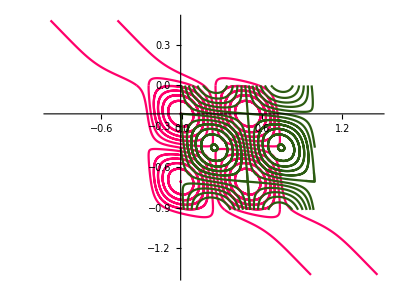

```mathematica
pl2=Show[pl1,Table[ParametricPlot[Evaluate[{tg[s],zg[s]}/.SPG[[i,1,1]]],{s,0,SPG[[i,2]]},PlotStyle->plstyl],{i,1,Length[SPG]}],Table[ParametricPlot[Evaluate[{tg[s],zg[s]}/.SPG1[[i,1,1]]],{s,0,SPG1[[i,2]]},PlotStyle->plstyl],{i,1,Length[SPG1]}],Table[ParametricPlot[Evaluate[{tg[s],zg[s]}/.SPG10[[i,1,1]]],{s,0,SPG10[[i,2]]},PlotStyle->plstyl],{i,1,Length[SPG10]}],Table[ParametricPlot[Evaluate[{tg[s],zg[s]}/.SPG2[[i,1,1]]],{s,0,SPG2[[i,2]]},PlotStyle->plstyl],{i,1,Length[SPG2]}],Table[ParametricPlot[Evaluate[{tg[s],zg[s]}/.SPG20[[i,1,1]]],{s,0,SPG20[[i,2]]},PlotStyle->plstyl],{i,1,Length[SPG20]}],ParametricPlot[Evaluate[{tg[s],zg[s]}/.spigt2[[1,1]]],{s,0,spigt2[[2]]},PlotStyle->plstyl],PlotRange->All]
```

```mathematica
sArP={{tg[SPG[[13,2]]],zg[SPG[[13,2]]],ϕg[SPG[[13,2]]]}/.SPG[[13,1,1]]};
Do[If[(zg[SPG1[[i,2]]]/.SPG1[[i,1,1]])>-0.01,AppendTo[sArP,{tg[SPG1[[i,2]]],zg[SPG1[[i,2]]],ϕg[SPG1[[i,2]]]}/.SPG1[[i,1,1]]]],{i,1,Length[SPG1]}];
Do[If[(zg[SPG10[[i,2]]]/.SPG10[[i,1,1]])>-0.01,AppendTo[sArP,{tg[SPG10[[i,2]]],zg[SPG10[[i,2]]],ϕg[SPG10[[i,2]]]}/.SPG10[[i,1,1]]]],{i,1,Length[SPG10]}];
sArP=SortBy[AppendTo[sArP,{t[sppa0],z[sppa0]}/.MSPAR[[3,1,1]]],First];
sATp={{tg[SPG[[16,2]]],zg[SPG[[16,2]]],ϕg[SPG[[16,2]]]}/.SPG[[16,1,1]]};
Do[If[(zg[SPG2[[i,2]]]/.SPG2[[i,1,1]])<-0.9,AppendTo[sATp,{tg[SPG2[[i,2]]],zg[SPG2[[i,2]]],ϕg[SPG2[[i,2]]]}/.SPG2[[i,1,1]]]],{i,1,Length[SPG2]}];
Do[If[(zg[SPG20[[i,2]]]/.SPG20[[i,1,1]])<-0.9,AppendTo[sATp,{tg[SPG20[[i,2]]],zg[SPG20[[i,2]]],ϕg[SPG20[[i,2]]]}/.SPG20[[i,1,1]]]],{i,1,Length[SPG20]}];
Do[If[sATp[[i,2]]>-0.915,sATp[[i]]=({tg[spigt2[[2]]],zg[spigt2[[2]]],ϕg[spigt2[[2]]]}/.spigt2[[1,1]])],{i,1,Length[sATp]}];(*please, pay attention that here I replase one point because of some problem with SPG20[[2]](it stops earlier than it should) *)
sATp=SortBy[sATp,First];
```

```mathematica
(*Stop points for the integration for ES in the air above the slits.*)
vFESinAr=Flatten[{0.85,1,1.4,3.5,2,2,0.5,0.85,0.85,0.85,0.9,0.95,1.2,1.5,2,8,5,5,Table[0.85,{i,1,5}]},1];
(*Solution of the differential equations to find ES lines above the slits. The procedure "Needs" allows to extract stop points for some of lines.*)
sissi=-1;
Clear[SPA1,sf];
SPA1=Table[{NDSolve[{t'[s]==sissi ftAr[t[s],x[s],z[s]],x'[s]==sissi fxAr[t[s],x[s],z[s]],z'[s]==sissi fzAr[t[s],x[s],z[s]],ϕ'[s]==sissi((hyAr[t[s],x[s],z[s]])^2-(exAr[t[s],x[s],z[s]])^2-(ezAr[t[s],x[s],z[s]])^2),t[0]==sArP[[i,1]],x[0]==XC,z[0]==sArP[[i,2]],ϕ[0]==sArP[[i,3]], WhenEvent[z[s]<-10^-5,end=s;sf=s;"StopIntegration"]},{t,x,z,ϕ},{s,0,vFESinAr[[i]]}(*,Method->{"EquationSimplification"->{Automatic,
"SimplifySystem"->True}}*)],sf},{i,8,18}];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
sissi=-1;
Clear[SPA10];
SPA10=Quiet[Table[InterpolatingFunctionDomain[First[t/.NDSolve[{t'[s]==sissi ftAr[t[s],x[s],z[s]],x'[s]==sissi fxAr[t[s],x[s],z[s]],z'[s]==sissi fzAr[t[s],x[s],z[s]],ϕ'[s]==sissi((hyAr[t[s],x[s],z[s]])^2-(exAr[t[s],x[s],z[s]])^2-(ezAr[t[s],x[s],z[s]])^2),t[0]==sArP[[i,1]],x[0]==XC,z[0]==sArP[[i,2]],ϕ[0]==sArP[[i,3]], WhenEvent[z[s]<-10^-5,end=s;sf=s;"StopIntegration"]},{t,x,z,ϕ},{s,0,vFESinAr[[i]]}]]][[1,2]],{i,8,18}]];
Do[SPA1[[i,2]]=SPA10[[i]],{i,1,Length[SPA1]}];
sissi=1;
Clear[SPA2,sf];
SPA2=Table[{NDSolve[{t'[s]==sissi ftAr[t[s],x[s],z[s]],x'[s]==sissi fxAr[t[s],x[s],z[s]],z'[s]==sissi fzAr[t[s],x[s],z[s]],ϕ'[s]==sissi((hyAr[t[s],x[s],z[s]])^2-(exAr[t[s],x[s],z[s]])^2-(ezAr[t[s],x[s],z[s]])^2),t[0]==sArP[[i,1]],x[0]==XC,z[0]==sArP[[i,2]],ϕ[0]==sArP[[i,3]], WhenEvent[z[s]<-10^-5,end=s;sf=s;"StopIntegration"]},{t,x,z,ϕ},{s,0,vFESinAr[[i]]}(*,Method->{"EquationSimplification"->{Automatic,
"SimplifySystem"->True}}*)],sf},{i,Join[Range[1,6],Range[16,Length[sArP]]]}];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
sissi=1;
Clear[SPA20];
SPA20=Quiet[Table[InterpolatingFunctionDomain[First[t/.NDSolve[{t'[s]==sissi ftAr[t[s],x[s],z[s]],x'[s]==sissi fxAr[t[s],x[s],z[s]],z'[s]==sissi fzAr[t[s],x[s],z[s]],ϕ'[s]==sissi((hyAr[t[s],x[s],z[s]])^2-(exAr[t[s],x[s],z[s]])^2-(ezAr[t[s],x[s],z[s]])^2),t[0]==sArP[[i,1]],x[0]==XC,z[0]==sArP[[i,2]],ϕ[0]==sArP[[i,3]], WhenEvent[z[s]<-10^-5,end=s;sf=s;"StopIntegration"]},{t,x,z,ϕ},{s,0,vFESinAr[[i]]}]]][[1,2]],{i,Join[Range[1,6],Range[16,Length[sArP]]]}]];
Do[SPA2[[i,2]]=SPA20[[i]],{i,1,Length[SPA2]}];
```

```mathematica
(*Stop points for the integration for ES in the air above the slits.*)
vFESinAt1=Flatten[{Table[0.85,{i,1,4}],2.5,3.5,2,1.3,1.1,0.9,Table[0.85,{i,1,5}],2,2.5,4,1.2,0.9,0.85},1];
(*Solution of the differential equations to find ES lines below the slits. The procedure "Needs" allows to extract stop points for some of lines.*)
sissi=-1;
Clear[SPA3,sf];
SPA3=Table[{NDSolve[{t'[s]==sissi ftAt[t[s],x[s],z[s]],x'[s]==0,z'[s]==sissi fzAt[t[s],x[s],z[s]],ϕ'[s]==sissi((hyAt[t[s],x[s],z[s]])^2-(exAt[t[s],x[s],z[s]])^2-(ezAt[t[s],x[s],z[s]])^2),t[0]==sATp[[i,1]],x[0]==XC,z[0]==sATp[[i,2]],ϕ[0]==sATp[[i,3]], WhenEvent[z[s]<-10^-5,end=s;sf=s;"StopIntegration"]},{t,x,z,ϕ},{s,0,vFESinAt1[[i]]}(*,Method->{"EquationSimplification"->{Automatic,
"SimplifySystem"->True}}*)],sf},{i,Join[{1,2,3,4},Range[16,Length[sATp]]]}];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
sissi=-1;
Clear[SPA30];
SPA30=Quiet[Table[InterpolatingFunctionDomain[First[t/.NDSolve[{t'[s]==sissi ftAt[t[s],x[s],z[s]],x'[s]==0,z'[s]==sissi fzAt[t[s],x[s],z[s]],ϕ'[s]==sissi((hyAt[t[s],x[s],z[s]])^2-(exAt[t[s],x[s],z[s]])^2-(ezAt[t[s],x[s],z[s]])^2),t[0]==sATp[[i,1]],x[0]==XC,z[0]==sATp[[i,2]],ϕ[0]==sATp[[i,3]], WhenEvent[z[s]<-10^-5,end=s;sf=s;"StopIntegration"]},{t,x,z,ϕ},{s,0,vFESinAt1[[i]]}]]][[1,2]],{i,Join[{1,2,3,4},Range[16,Length[sATp]]]}]];
Do[SPA3[[i,2]]=SPA30[[i]],{i,1,Length[SPA3]}];
sissi=1;
Clear[SPA4,sf];
SPA4=Table[{NDSolve[{t'[s]==sissi ftAt[t[s],x[s],z[s]],x'[s]==0,z'[s]==sissi fzAt[t[s],x[s],z[s]],ϕ'[s]==sissi((hyAt[t[s],x[s],z[s]])^2-(exAt[t[s],x[s],z[s]])^2-(ezAt[t[s],x[s],z[s]])^2),t[0]==sATp[[i,1]],x[0]==XC,z[0]==sATp[[i,2]],ϕ[0]==sATp[[i,3]], WhenEvent[z[s]<-10^-5,end=s;sf=s;"StopIntegration"]},{t,x,z,ϕ},{s,0,vFESinAt1[[i]]}(*,Method->{"EquationSimplification"->{Automatic,
"SimplifySystem"->True}}*)],sf},{i,Range[5,15]}];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
sissi=1;
Clear[SPA40];
SPA40=Quiet[Table[InterpolatingFunctionDomain[First[t/.NDSolve[{t'[s]==sissi ftAt[t[s],x[s],z[s]],x'[s]==0,z'[s]==sissi fzAt[t[s],x[s],z[s]],ϕ'[s]==sissi((hyAt[t[s],x[s],z[s]])^2-(exAt[t[s],x[s],z[s]])^2-(ezAt[t[s],x[s],z[s]])^2),t[0]==sATp[[i,1]],x[0]==XC,z[0]==sATp[[i,2]],ϕ[0]==sATp[[i,3]], WhenEvent[z[s]<-10^-5,end=s;sf=s;"StopIntegration"]},{t,x,z,ϕ},{s,0,vFESinAt1[[i]]}]]][[1,2]],{i,Range[5,15]}]];
Do[SPA4[[i,2]]=SPA40[[i]],{i,1,Length[SPA4]}];
```

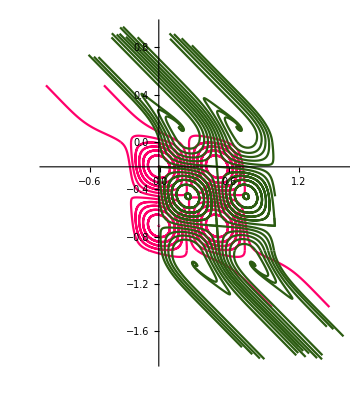

```mathematica
pl3=Show[pl2,Table[ParametricPlot[Evaluate[{t[s],z[s]}/.SPA1[[i,1,1]]],{s,0,SPA1[[i,2]]},PlotStyle->plstyl],{i,1,Length[SPA1]}],Table[ParametricPlot[Evaluate[{t[s],z[s]}/.SPA2[[i,1,1]]],{s,0,SPA2[[i,2]]},PlotStyle->plstyl],{i,1,Length[SPA2]}],Table[ParametricPlot[Evaluate[{t[s],z[s]}/.SPA3[[i,1,1]]],{s,0,SPA3[[i,2]]},PlotStyle->plstyl],{i,1,Length[SPA3]}],Table[ParametricPlot[Evaluate[{t[s],z[s]}/.SPA4[[i,1,1]]],{s,0,SPA4[[i,2]]},PlotStyle->plstyl],{i,1,Length[SPA4]}]]
```

## Red lines with another flux step

We continue in air with flux step six time smaller to show the contrast between flux intensity in the slit and air region

```mathematica
elFlintAr[z_,t1_,t2_]:= Re[HyAr[XC,z] ⅈ/k0( Exp[-ⅈ k0 t2]- Exp[-ⅈ k0 t1])];
tt0zpieft=t[MSPAR[[2,2]]]/.MSPAR[[2,1,1]];
zz0zpieft=z[MSPAR[[2,2]]]/.MSPAR[[2,1,1]];
ieft=Table[{t,elFlintAr[zz0zpieft,tt0zpieft,t]},{t,tt0zpieft,0.022,0.02}];
ieff=Interpolation[ieft];
def=δfiE/6;
FindMaximum[ieff[t],{t,-0.25,tt0zpieft,0.022}][[1]]/def;
spMSNz=Sort[Join[Table[FindRoot[ieff[t]-i def==0,{t,-0.4,tt0zpieft,0.022}][[1,2]],{i,1,5}],Table[FindRoot[ieff[t]-i def==0,{t,-0.1,tt0zpieft,0.022}][[1,2]],{i,1,5}]]];
sf=0;
Clear[MSPAN1];
sissi=1; 
MSPAN1=Table[{NDSolve[{t'[s]==sissi fzAr[t[s],x[s],z[s]],x'[s]==0,z'[s]==sissi ftAr[t[s],x[s],z[s]],t[0]==spMSNz[[i]],x[0]==XC ,z[0]==zz0zpieft, WhenEvent[z[s]<-10^-5,end=s;sf=s;"StopIntegration"]},{t,x,z},{s,0,1.75}],sf},{i,1,5}];
MSPAN1[[5,2]]=1.75;
sf=0;
Clear[MSPAN2];
sissi=-1; 
MSPAN2=Table[{NDSolve[{t'[s]==sissi fzAr[t[s],x[s],z[s]],x'[s]==0,z'[s]==sissi ftAr[t[s],x[s],z[s]],t[0]==spMSNz[[i]],x[0]==XC ,z[0]==zz0zpieft, WhenEvent[z[s]<-10^-5,end=s;sf=s;"StopIntegration"]},{t,x,z},{s,0,0.8}],sf},{i,7,Length[spMSNz]}];
sfg=0;
Clear[MSPG2];
sissi=1; MSPG2=Table[{NDSolve[{tg'[sg]==sissi fzG[tg[sg],xg[sg],zg[sg]],xg'[sg]==0,zg'[sg]==sissi ftG[tg[sg],xg[sg],zg[sg]],tg[0]==(t[MSPAN1[[i,2]]]/.MSPAN1[[i,1,1]]),xg[0]==XC,zg[0]==(z[MSPAN1[[i,2]]]/.MSPAN1[[i,1,1]]), WhenEvent[zg[sg]>10^-7∨zg[sg]<-h0,end=sg;sfg=sg;"StopIntegration"]},{tg,xg,zg},{sg,0,0.5}],sfg},{i,1,4}];
sfg=0;
Clear[MSPG20];
sissi=-1; MSPG20=Table[{NDSolve[{tg'[sg]==sissi fzG[tg[sg],xg[sg],zg[sg]],xg'[sg]==0,zg'[sg]==sissi ftG[tg[sg],xg[sg],zg[sg]],tg[0]==(t[MSPAN2[[i,2]]]/.MSPAN2[[i,1,1]]),xg[0]==XC,zg[0]==(z[MSPAN2[[i,2]]]/.MSPAN2[[i,1,1]]), WhenEvent[zg[sg]>10^-7∨zg[sg]<-h0,end=sg;sfg=sg;
"StopIntegration"]},{tg,xg,zg},{sg,0,0.3}],sfg},{i,1,4}];
MSPG20[[1,2]]=0.2881241997488341;
MSPG20[[4,2]]=0.26659821009394813;

sf=0;
Clear[MSPAT1];
sissi=1; 
MSPAT1=Table[{NDSolve[{t'[s]==sissi fzAt[t[s],x[s],z[s]],x'[s]==0,z'[s]==sissi ftAt[t[s],x[s],z[s]],t[0]==(tg[MSPG2[[i,2]]]/.MSPG2[[i,1,1]]),x[0]==XC ,z[0]==(zg[MSPG2[[i,2]]]/.MSPG2[[i,1,1]]), WhenEvent[z[s]<-10^-5,end=s;sf=s;"StopIntegration"]},{t,x,z},{s,0,0.5}],sf},{i,1,Length[MSPG2]}];
Do[MSPAT1[[i,2]]=0.5,{i,1,Length[MSPAT1]}];

sissi=-1; 
mspp0={NDSolve[{tg'[sg]==sissi fzG[tg[sg],xg[sg],zg[sg]],xg'[sg]==0,zg'[sg]==sissi ftG[tg[sg],xg[sg],zg[sg]],tg[0]==(tg[MSPG20[[4,2]]]/.MSPG20[[4,1,1]]),xg[0]==XC,zg[0]==(zg[MSPG20[[4,2]]]/.MSPG20[[4,1,1]]), WhenEvent[zg[sg]>10^-7∨zg[sg]<-h0,end=sg;sfg=sg;
"StopIntegration"]},{tg,xg,zg},{sg,0,0.3}],sfg};
sf=0;
Clear[MSPAT2];
sissi=-1; 
MSPAT2=Table[{NDSolve[{t'[s]==sissi fzAt[t[s],x[s],z[s]],x'[s]==0,z'[s]==sissi ftAt[t[s],x[s],z[s]],t[0]==(tg[MSPG20[[i,2]]]/.MSPG20[[i,1,1]]),x[0]==XC ,z[0]==(zg[MSPG20[[i,2]]]/.MSPG20[[i,1,1]]), WhenEvent[z[s]<-10^-5,end=s;sf=s;"StopIntegration"]},{t,x,z},{s,0,0.5}],sf},{i,1,3}];
MSPAT2=Join[MSPAT2,{{NDSolve[{t'[s]==sissi fzAt[t[s],x[s],z[s]],x'[s]==0,z'[s]==sissi ftAt[t[s],x[s],z[s]],t[0]==(tg[mspp0[[2]]]/.mspp0[[1,1]]),x[0]==XC ,z[0]==(zg[mspp0[[2]]]/.mspp0[[1,1]]), WhenEvent[z[s]<-10^-5,end=s;sf=s;"StopIntegration"]},{t,x,z},{s,0,0.5}],sf}}];
Do[MSPAT2[[i,2]]=0.5,{i,1,Length[MSPAT2]}];
```

## Final plot

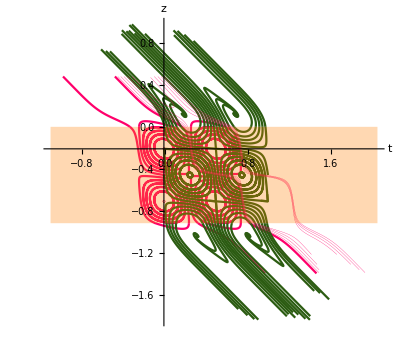

```mathematica
plstyln={Thickness[0.0005],Hue[0.93]};
pl40=Show[pl3,Table[ParametricPlot[Evaluate[{t[s],z[s]}/.MSPAN1[[i,1,1]]],{s,0,MSPAN1[[i,2]]},PlotStyle->plstyln],{i,1,Length[MSPAN1]}],Table[ParametricPlot[Evaluate[{t[s],z[s]}/.MSPAN2[[i,1,1]]],{s,0,MSPAN2[[i,2]]},PlotStyle->plstyln],{i,1,Length[MSPAN2]}],Table[ParametricPlot[Evaluate[{tg[s],zg[s]}/.MSPG2[[i,1,1]]],{s,0,MSPG2[[i,2]]},PlotStyle->plstyln],{i,1,Length[MSPG2]}],Table[ParametricPlot[Evaluate[{tg[s],zg[s]}/.MSPG20[[i,1,1]]],{s,0,MSPG20[[i,2]]},PlotStyle->plstyln],{i,1,Length[MSPG20]}],ParametricPlot[Evaluate[{tg[s],zg[s]}/.mspp0[[1,1]]],{s,0,mspp0[[2]]},PlotStyle->plstyln],Table[ParametricPlot[Evaluate[{t[s],z[s]}/.MSPAT1[[i,1,1]]],{s,0,MSPAT1[[i,2]]},PlotStyle->plstyln],{i,1,Length[MSPAT1]}],Table[ParametricPlot[Evaluate[{t[s],z[s]}/.MSPAT2[[i,1,1]]],{s,0,MSPAT2[[i,2]]},PlotStyle->plstyln],{i,1,Length[MSPAT2]}],Graphics[{Orange,Opacity[.3],Polygon[{{-1.1,0},{2.05,0},{2.05,-h0},{-1.1,-h0}}]}],PlotRange->All,AxesLabel->{"t","z"},AxesStyle->Directive[18,Black]]
```

## How we find Z0 & Z1

Please, uncomment this section if you'd like to run it

```mathematica
(*zz0=ParallelTable[{z,elFlinzG[τ0[[1]],-h0,z]},{z,-h0,0,h0/50}]
zz1=ParallelTable[{z,elFlinzG[-0.01,-h0,z]},{z,-h0,0,h0/50}]
zz2=ParallelTable[{z,elFlinzG[0.01,-h0,z]},{z,-h0,0,h0/50}]
zz0In=Interpolation[zz0]
zz1In=Interpolation[zz1]
zz2In=Interpolation[zz2]*)
```

```mathematica
(*zz0Max=FindMaximum[zz0In[z],{z,-0.2}]
zz0Min=FindMinimum[zz0In[z],{z,-0.7}]
zz1Max=FindMaximum[zz1In[z],{z,-0.2}]
zz1Min=FindMinimum[zz1In[z],{z,-0.7}]
zz2Max=FindMaximum[zz2In[z],{z,-0.2}]
zz2Min=FindMinimum[zz2In[z],{z,-0.7}]
zz0d=zz0Max[[1]]-zz0Min[[1]]
zz1d=zz1Max[[1]]-zz1Min[[1]]
zz2d=zz2Max[[1]]-zz2Min[[1]]
centZ0=zz0Max[[2,1,2]]*)
```

```mathematica
(*ttz=ParallelTable[{t,z,elFlintG[z,-0.05,t]},{t,-0.05,0.05,0.001},{z,-0.3,-0.1,0.005}]*)
```

```mathematica
(*zz0=ParallelTable[{z,elFlinzG[-0.0002,-h0,z]},{z,-h0,0,h0/50}];
zz0In=Interpolation[zz0];
zz0Max=FindMaximum[zz0In[z],{z,-0.2}];
zz0Min=FindMinimum[zz0In[z],{z,-0.7}];
centZ0=zz0Max[[2,1,2]]*)
```